# Fourier discrete sine transform

```mathematica
Needs["FourierSeries`"]
```

```mathematica
Clear["Global`*"]
```

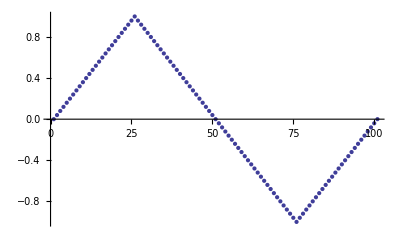

```mathematica
data=Table[TriangleWave[{-1,1},x],{x,0,1,0.01}];
n=Length[data];
ListPlot[data]
```

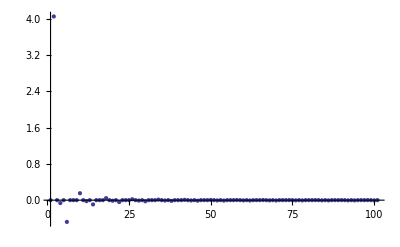

```mathematica
dct=FourierDST[data];
ListPlot[dct,PlotRange->All]
```

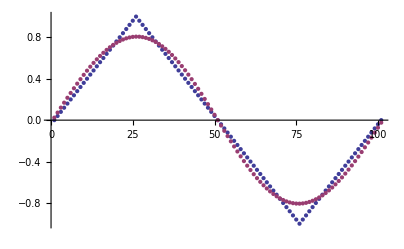

```mathematica
tdata=FourierDST[PadRight[Take[dct,5],n,0],3];
ListPlot[{data,tdata}]
```